1. Naloga

a)

```mathematica
Izraz = (x^5 - 2x^2+3x+4)/(x^5-2x-1)
Izraz /.x->1
Izraz /.x->2
Izraz /.x->3
Izraz /.x->4
```

(4+3 x-2 x^2+x^5)/(-1-2 x+x^5)

-3

34/27

119/118

144/145

b)

```mathematica
f[x_] :=(x^5 - 2x^2+3x+4)/(x^5-2x-1)
f[1]
f[2]
f[3]
f[4]
```

-3

34/27

119/118

144/145

```mathematica
Table[f[x], {x, 1, 4}]
```

{-3,34/27,119/118,144/145}

2. Naloga

```mathematica
sez = {10, 20, 30, 40, 50, 60, 70}
```

{10,20,30,40,50,60,70}

a)

```mathematica
Take[sez, 3]
```

{10,20,30}

b)

```mathematica
Take[sez, -2]
```

{60,70}

c)

```mathematica
Rest[Drop[sez, -3]]
```

{20,30,40}

d)

```mathematica
Part[sez, 2]
sez[[3]]
Part[sez, 5]
```

20

30

50

e)

```mathematica
Drop[sez, {4,5}]
```

{10,20,30,60,70}

3. Naloga

```mathematica
sez = {x^6, x^2, a}
```

{x^6,x^2,a}

a)

```mathematica
sez /. x->3
```

{729,9,a}

b)

```mathematica
sez /. x->x^2
```

{x^12,x^4,a}

c)

```mathematica
sez /. x^2->x
```

{x^6,x,a}

d)

```mathematica
sez /. x->{1,2,3}
```

{{1,64,729},{1,4,9},a}

e)

```mathematica
sez /.{x->3 ,a->x}
```

{729,9,x}

f)

```mathematica
ReplaceRepeated[sez , {x->3 ,a->x}]
```

{729,9,3}

4. Naloga

a)

```mathematica
f[x_]:=x^5+4x^3+9
D[f[x], x]
f'[1]
f'[5]
```

12 x^2+5 x^4

17

3425

```mathematica
∈
```

b)

```mathematica
f[x_]:=E^Surd[x,4]
D[f[x], x]
f'[1]
f'[2]
```

(ⅇ^(x^(1/4)))/(4 (x^(1/4))^3)

ⅇ/4

(ⅇ^(2^(1/4)))/(4 2^(3/4))

c)

```mathematica
f[x_]:=Abs[x+1]
FullSimplify[D[f[x], x], x∈Reals]
f'[1]
f'[-1]
```

Sign[1+x]

Abs'[2]

Abs'[0]

d)

```mathematica
Clear[a,b]
```

```mathematica
f[x_]:=a*x^2+3b
D[f[x], x]
f'[1]
f'[2]
```

2 a x

2 a

4 a

5. Naloga

a)

```mathematica
f[x_]:=x^3*Log[4x+5 ]
```

b)

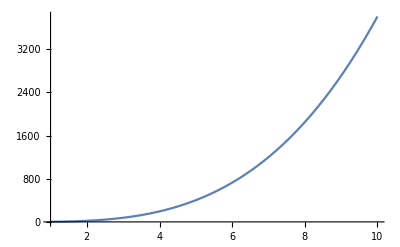

```mathematica
Plot[f[x], {x, 1, 10}]
```

c)

```mathematica
f[5]
```

125 Log[25]

d)

```mathematica
K=f'[5]
```

20+75 Log[25]

e)

```mathematica
t[x_]:=K *(x-5)+f[5]
```

```mathematica
t[0]
```

125 Log[25]-5 (20+75 Log[25])

f)

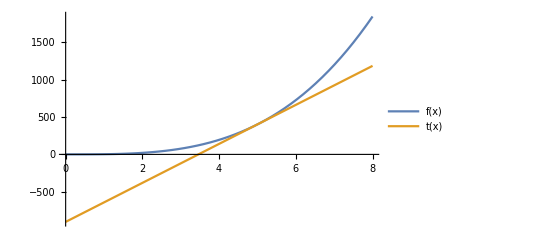

```mathematica
Plot[{f[x], t[x]}, {x, 0, 8}, PlotLegends->"Expressions"]
```

g)

```mathematica
narisi[x0_]:=Module[{k0, n0, t},
k0 = D[f[x], x]/. x ->x0;
n0=n/. First[Solve[f[x0]==k0*x0+n, n]];
t[x_]:=k0*x+n0;
Plot[{f[x], t[x]}, {x, 1, 10}]
]

Manipulate[narisi[x0, Sin], {x0, 1, 10}]
```

6. Naloga

a)

```mathematica
Limit[(x^3-4x^2+2x+4)/(x^5-9x-14),x-> 2]
```

-2/71

b)

```mathematica
Limit[ArcTan[7x]/ArcTan[8x], x->0]
```

7/8

c)

```mathematica
Limit[(x^2-25)Cot[Pi*x], x->5]
```

10/π

d)

```mathematica
Limit[(1+Cos[x])/(2Sqrt[Pi*x]-Pi-x), x-> Pi]
```

-2 π

e)

```mathematica
Limit[Abs[x]Cot[x], x->0, Direction->1]
```

-1

f)

```mathematica
Limit[Abs[x]Cot[x], x->0, Direction->-1]
```

1

7. Naloga

```mathematica
f[x_]:=(x^2-1)/(x^2-4)
```

a)

```mathematica
Solve[f[x]==0]
```

{{x→-1},{x→1}}

Funkcija ima ničle pri x = -1 in x = 1.

b)

```mathematica
Solve[Denominator[f[x]]==0]
```

{{x→-2},{x→2}}

Funkcija ima pola pri x = -2 in x = 2.

```mathematica
Limit[f[x], x->2, Direction->1]
Limit[f[x], x->2, Direction->-1]
Limit[f[x], x->-2, Direction->1]
Limit[f[x], x->-2, Direction->-1]
```

-∞

∞

∞

-∞

c)

```mathematica
a[x_]:=PolynomialQuotient[Numerator[f[x]], Denominator[f[x]],x]
a[x]
```

1

Asimptota funkcije je premica y = 1.

d)

```mathematica
Solve[D[f[x],x]==0]
```

{{x→0}}

Funkcija ima ekstrem pri x = 0.

e)

```mathematica
Solve[f''[x]==0]
```

{{x→-(2 ⅈ)/(√3)},{x→(2 ⅈ)/(√3)}}

Funkcija nima prevojev.

f)

```mathematica
Reduce[f''[x]>0]
Reduce[f''[x]<0]
```

x<-2||x>2

-2<x<2

Funcija je konveksna na intervalu (-∞, -2) ∪ (2, ∞).

Funcija je konkavna na intervalu (-2,2).

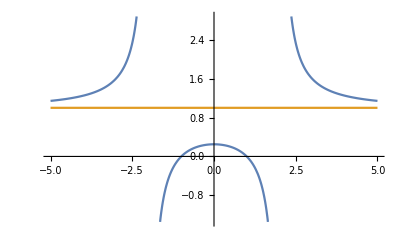

```mathematica
Plot[{f[x], 1,}, {x, -5, 5}]
```

8. Naloga

```mathematica
Solve[{x^4+x^3-x==0, x>0},x]
```

{{x→Root[-1+#1^2+#1^3&,1]}}

9. Naloga

```mathematica
Solve[{3x^2-5y^2==5, 2x^2+3y^2==59}]
```

{{x→-√(310/19),y→-√(167/19)},{x→-√(310/19),y→√(167/19)},{x→√(310/19),y→-√(167/19)},{x→√(310/19),y→√(167/19)}}